```mathematica
Sum[1/k n^k/(k!),{k,1,∞}]
```

-EulerGamma-Gamma[0,-n]-Log[-n]

```mathematica
FullSimplify[-Gamma[0,-n]-Log[-n],n>=0]
```

ExpIntegralEi[n]-Log[n]

```mathematica
bias[n_]=(Exp[-n](1-EulerGamma+ExpIntegralEi[n]-Log[n]))^-1-n
```

-n+ⅇ^n/(1-EulerGamma+ExpIntegralEi[n]-Log[n])

```mathematica
N[bias[0.5]]
```

0.55004

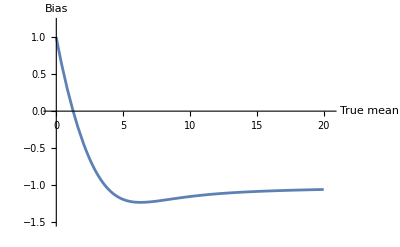

```mathematica
Plot[
N[bias[n]],
{n,0.0,20.0},
PlotRange->{{-0.5,20.5},{-1.5,1.2}},
AxesLabel->{"True mean","Bias"}
]
```